```mathematica
Series[(1+dm)^(1-τ λ),{dm,0,1}]
```

1+(1-λ τ) dm+O[dm]^2

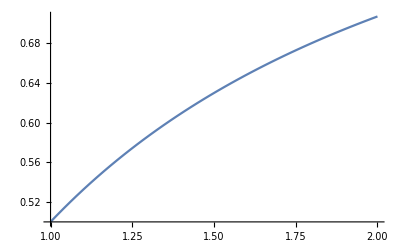

```mathematica
Plot[2^(-1/k),{k,1,2}]
```

```mathematica
Solve[α x + ρ1 b - α x(m+x)==0,x]//Simplify
```

{{x→1/2 (1-m-(√((-1+m)^2 α+4 b ρ1))/(√α))},{x→1/2 (1-m+(√((-1+m)^2 α+4 b ρ1))/(√α))}}

```mathematica
DSolve[y'[t]== r Exp[(α+β)t],y[t],t]
```

{{y[t]→(ⅇ^(t (α+β)) r)/(α+β)+C[1]}}

```mathematica
DSolve[{nr'[t]==α nr[t] + (r1 α (Exp[(α-β t)]-Exp[-r t]) β nm0)/(α-β + r),nr[0]==0},nr[t],t]//Simplify
```

{{nr[t]→(ⅇ^(-t (r+β)) nm0 r1 α β (-ⅇ^(r t+α) (r+α)+ⅇ^(α+t (r+α+β)) (r+α)+ⅇ^(t β) (α+β)-ⅇ^(t (r+α+β)) (α+β)))/((r+α) (r+α-β) (α+β))}}

```mathematica
(ⅇ^(-t (r+β)) nm0 r1 α β (-ⅇ^(r t+α) (r+α)+ⅇ^(α+t (r+α+β)) (r+α)+ⅇ^(t β) (α+β)-ⅇ^(t (r+α+β)) (α+β)))/((r+α) (r+α-β) (α+β))
```

```mathematica
DSolve[{pr'[t]== α pr[t] + r1 pb[t]-α pr[t](pm[t]+pr[t]),
pb'[t]== β pm[t] + r pb[t]-α pr[t](pm[t]+pr[t]),
pb'[t]== β pm[t] + r pb[t]-α pr[t](pm[t]+pr[t])},{pr[t],pb[t],pm[t]}]
```